```mathematica
Clear["Global`*"]
g=9.81;
maxAngle=theta/.(Solve[2*V^2/g*Cos[2*theta]==0,theta][[2]]);
maxAngleDeg = maxAngle*180/Pi
vel=V/.(Solve[2*V^2/g*Sin[2*maxAngle]==1000, V][[2]])
vx = vel*Cos[maxAngle]
vy = vel*Sin[maxAngle]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

45.

70.0357

49.5227

49.5227

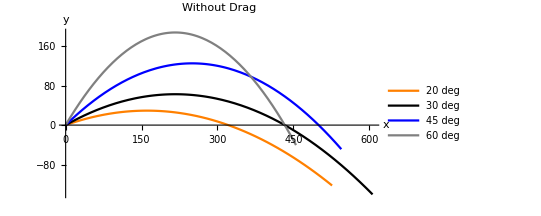

```mathematica
Clear["Global`*"]
m=1;
g=9.81;
vel=70.03570517957252;

eqs = {x''[t]==0, y''[t]==-g};

(*20 deg*)
ini1= {x[0]==0, y[0]==0, x'[0]==vel * Cos[20.*Pi/180.], y'[0]==vel *  Sin[20.*Pi/180.]} ;
soln1=NDSolve[Join [eqs, ini1], {x,y}, {t, 0, 15}];

(*30 deg*)
ini2= {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/6.], y'[0]==vel * Sin[Pi/6.]} ;
soln2=NDSolve[Join [eqs, ini2], {x,y}, {t, 0, 15}];

(*45 deg*)
ini3= {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/4.], y'[0]==vel * Sin[Pi/4.]} ;
soln3=NDSolve[Join [eqs, ini3], {x,y}, {t, 0, 15}];

(*60 deg*)
ini4= {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/3.], y'[0]==vel * Sin[Pi/3.]} ;
soln4=NDSolve[Join [eqs, ini4], {x,y}, {t, 0, 15}];

p1=ParametricPlot[{x[t], y[t]}/.soln1, {t, 0,8},
	PlotLegends->{"20 deg"},
	PlotStyle->Orange];

p2=ParametricPlot[{x[t], y[t]}/.soln2, {t, 0,10},
	PlotLegends->{"30 deg"},
	PlotStyle->Black];

p3=ParametricPlot[{x[t], y[t]}/.soln3, {t, 0,11},
	PlotLegends->{"45 deg"},
	PlotStyle->Blue];

p4=ParametricPlot[{x[t], y[t]}/.soln4, {t, 0,13},
	PlotLegends->{"60 deg"},
	PlotStyle->Gray];

Show[{p1, p2, p3, p4}, AxesLabel->{x, y},PlotRange->All, PlotLabel->"Without Drag"]
```

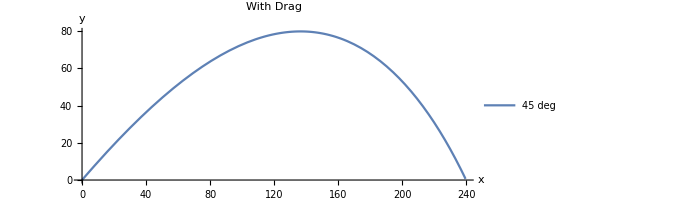

```mathematica
Clear["Global`*"]
v=Sqrt[x'[t]^2+y'[t]^2];
m=0.5;
g=9.81;
rho=1.3;
A=0.05^2/2;
vel=70.03570517957252;
drag = rho*A*v^2;

eqs = {x''[t]==-(drag/m )* (x'[t]/v), y''[t]==-g-(drag/m)(y'[t]/v)};
ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/4.], y'[0]==vel * Sin[Pi/4.]};
soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 15}];

ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 8},
	AxesLabel->{x, y},
	PlotLabel->"With Drag",
	PlotLegends->{"45 deg"}]
```

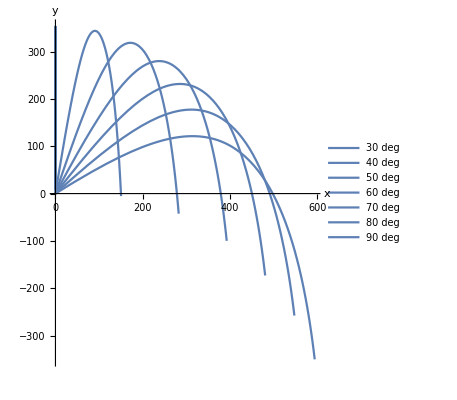

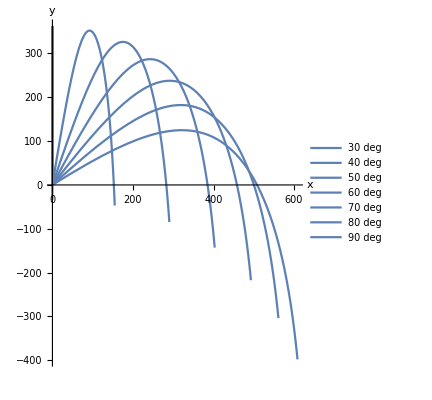

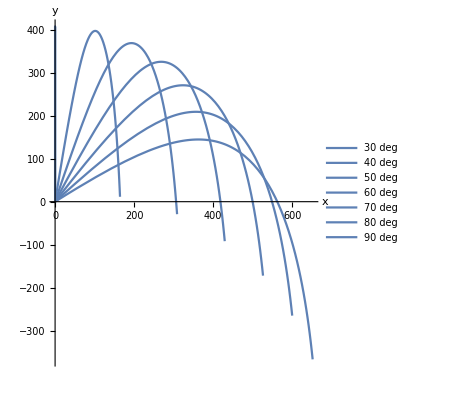

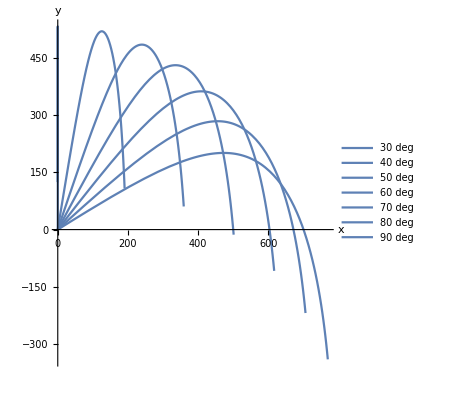

```mathematica
Clear["Global`*"]
v=Sqrt[x'[t]^2+y'[t]^2];
m=0.5;
g=9.81;
rho=1.3;
A=0.05^2/2;
vel=164;
drag = rho*A*v^2;

eqs = {x''[t]==-(drag/m )* (x'[t]/v), y''[t]==-g-(drag/m)(y'[t]/v)};

plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 20}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 17},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 30, 90, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All]

Clear[vel]
vel=169;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 20}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 18},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 30, 90, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All]

Clear[vel]
vel=199;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 20}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 18},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 30, 90, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All]

Clear[vel]
vel=305;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 20}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 19},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 30, 90, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All]
```

```mathematica
Clear["Global`*"]
v=Sqrt[x'[t]^2+y'[t]^2];
m=0.5;
g=9.81;
rho=1.3;
A=0.05^2/2;
drag = rho*A*v^2;

eqs = {x''[t]==-(drag/m )* (x'[t]/v), y''[t]==-g-(drag/m)(y'[t]/v)};

landTime[theta0_, v0_]:= 
Module[{theta=theta0, v=v0}, 
d = theta*Pi/180;
ini = {x[0]==0, y[0]==0, x'[0]==v * Cos[d],y'[0]==v* Sin[d]};
soln = NDSolve[Join [eqs, ini], {x,y}, {t, 0, 100}];
time=FindRoot[y[t]/.soln[[1,2]],{t,10}];
vals = {time, x/.soln[[1,1]]};
Return[vals]
]

range[theta0_, v0_]:=
Module[{theta=theta0, v=v0},
vals = landTime[theta, v];
time = vals[[1,1,2]];
x=vals[[2]];
distance = x[time];
Return[distance]
]

findVel[theta0_, Range_]:=
Module[{theta=theta0,x0=Range},
vStart = 0;
vEnd=100;
vHalf = (vStart+vEnd)/2.;
xMax = range[theta, vHalf];

While [xMax≠x0,
If[xMax>x0,{
Clear[vEnd, xMax];
vEnd=vHalf;
Clear[vHalf];
vHalf = (vStart+vEnd)/2.;
xMax= range[theta, vHalf];

},{
Clear[vStart, xMax];
vStart=vHalf;
Clear[vHalf];
vHalf = (vStart+vEnd)/2.;
xMax= range[theta, vHalf];

}]
];

Return[vHalf];
]

findVel[45,1000]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {«1»}.

ReplaceAll::reps: {y''[t]==-9.81-0.00325 y'[t] √((InterpolatingFunction[«5»][«1»])^2+((«1»)^(«1»)[«1»])^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {y''[10.]==-9.81-0.00325 y'[10.] √(131.663+((«1»)^(«1»)[«1»])^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {y[10.]/.y''[10.]==-9.81-0.00325 y'[10.] √(131.663+Power[«2»])} is not a list of numbers with dimensions {1} at {t} = {10.}.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {«1»}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

ReplaceAll::reps: {y''[t]==-9.81-0.00325 y'[t] √((InterpolatingFunction[«5»][«1»])^2+((«1»)^(«1»)[«1»])^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {y[10.]/.y''[10.]==-9.81-0.00325 y'[10.] √(131.663+Power[«2»])} is not a list of numbers with dimensions {1} at {t} = {10.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

75.

```mathematica
ScientificForm[75.]
```

7.5×10^1

```mathematica
NumberForm[75.]
```

75.

```mathematica
findMinAngle[Range]:=
Module[{x0=Range},
minVel = 0;

While[i<90,
testVel = findVel[i, x0];
If[testVel<minVel,{
Clear[minVel];
minVel = testVel;
angle= i
}, 1]
];
Return [angle];
]
```